Bessel

```mathematica
$Assumptions={τ>0,τR>0,t>=0,τ-t>=0};
```

```mathematica
(* Relaxation function *)
```

```mathematica
Psi[t_]=BesselJ[0,t/τR];
dPsi[t_]=D[Psi[t],t];
ddPsi[t_]=D[dPsi[t],t];
```

```mathematica
(* Dirac delta coefficient *)
```

```mathematica
f[s_]=-1/(s LaplaceTransform[ddPsi[t],t,s]);

c0=SeriesCoefficient[f[s],{s,0,0}];
```

```mathematica
(* Parameter and protocol *)
```

```mathematica
τR=1;

g[t_]=(t+τR)/(τ+2τR);
h1[t_]=t/τ;
dh1[t_]=h1'[t];
h2[t_]=(t/τ)^2;
dh2[t_]=h2'[t];
h3[t_]=(t/τ)^3;
dh3[t_]=h3'[t];
```

```mathematica
(* Calculation of the irreversible work *)
```

```mathematica
W0[τ_]=Psi[0]/2+Integrate[dPsi[τ-t]g[t],{t,0,τ}]-1/2 Integrate[ddPsi[t-u]g[t]g[u],{t,0,τ},{u,0,τ}];
```

```mathematica
W1[τ_]=W0[τ]+c0 dPsi[τ]/(τ+2τR)-c0/(τ+2τR)Integrate[ddPsi[t]g[t],{t,0,τ}]+c0/(τ+2τR)Integrate[ddPsi[τ-t]g[t],{t,0,τ}]-c0^2/(τ+2τR)^2 ddPsi[0]+c0^2/(τ+2τR)^2 ddPsi[τ];
```

```mathematica
Wh1[τ_]=1/2 Integrate[Psi[t-u]dh1[t]dh1[u],{t,0,τ},{u,0,τ}]
Wh2[t_]=Integrate[Psi[t-u]dh2[u],{u,0,t}];
Wh2[τ_]=Integrate[Wh2[t]dh2[t],{t,0,τ}]

Wh3[t_]=Integrate[Psi[t-u]dh3[u],{u,0,t}];
Wh3[τ_]=Integrate[Wh3[t]dh3[t],{t,0,τ}]
```

1/2 ((BesselJ[1,τ/τR] (-2 τR+π τ StruveH[0,τ/τR]))/τ+BesselJ[0,τ/τR] (2-π StruveH[1,τ/τR]))

(2 BesselJ[1,τ/τR] (-2 τR (τ^2+2 τR^2)+π τ^3 StruveH[0,τ/τR])+2 τ BesselJ[0,τ/τR] (2 (τ^2+τR^2)-π τ^2 StruveH[1,τ/τR]))/(3 τ^3)

1/(10 τ^6)3 (BesselJ[1,τ/τR] (-6 τ^5 τR+16 τ^3 τR^3-64 τ τR^5+π τ^4 (3 τ^2-5 τR^2) StruveH[0,τ/τR])+BesselJ[0,τ/τR] (6 τ^6-4 τ^4 τR^2+32 τ^2 τR^4+π (-3 τ^6+5 τ^4 τR^2) StruveH[1,τ/τR]))

```mathematica
(* Irreversible works *)
```

```mathematica
W0[τ_]=1/2+(τ^2+2 τ τR+2 τR^2-2 τR (τ+τR) BesselJ[0,τ/τR]-2 τ τR BesselJ[1,τ/τR])/(2 (τ+2 τR)^2)+(6 τR^2 (τ+τR) (-1+BesselJ[0,τ/τR])+τ^3 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2 (τ+2 τR));
W1[τ_]=1/2+τR^2/(2 (τ+2 τR)^2)+(τR^2 (-1+BesselJ[0,τ/τR]-BesselJ[1,τ/τR]))/(τ+2 τR)^2-(τR BesselJ[1,τ/τR])/(τ+2 τR)+(τ^2+2 τ τR+2 τR^2-2 τR (τ+τR) BesselJ[0,τ/τR]-2 τ τR BesselJ[1,τ/τR])/(2 (τ+2 τR)^2)+(τR (τR (-1+BesselJ[0,τ/τR])+(τ+τR) BesselJ[1,τ/τR]))/(τ+2 τR)^2-(τR^2 (BesselJ[0,τ/τR]-BesselJ[2,τ/τR]))/(2 (τ+2 τR)^2)+(6 τR^2 (τ+τR) (-1+BesselJ[0,τ/τR])+τ^3 HypergeometricPFQ[{3/2},{2,5/2},-τ^2/(4 τR^2)])/(6 τR^2 (τ+2 τR));
Wh1[τ_]=1/2 ((BesselJ[1,τ/τR] (-2 τR+π τ StruveH[0,τ/τR]))/τ+BesselJ[0,τ/τR] (2-π StruveH[1,τ/τR]));
Wh2[τ_]=(2 BesselJ[1,τ/τR] (-2 τR (τ^2+2 τR^2)+π τ^3 StruveH[0,τ/τR])+2 τ BesselJ[0,τ/τR] (2 (τ^2+τR^2)-π τ^2 StruveH[1,τ/τR]))/(3 τ^3);
Wh3[τ_]=1/(10 τ^6)3 (BesselJ[1,τ/τR] (-6 τ^5 τR+16 τ^3 τR^3-64 τ τR^5+π τ^4 (3 τ^2-5 τR^2) StruveH[0,τ/τR])+BesselJ[0,τ/τR] (6 τ^6-4 τ^4 τR^2+32 τ^2 τR^4+π (-3 τ^6+5 τ^4 τR^2) StruveH[1,τ/τR]));
```

```mathematica
(* Plot *)
```

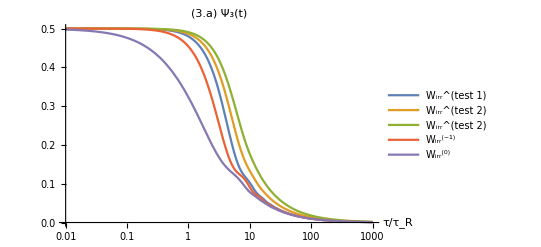

```mathematica
LogLinearPlot[{Legended[Wh1[τ],"W_irr^(test 1)"],Legended[Wh2[τ],"W_irr^(test 2)"],Legended[Wh3[τ],"W_irr^(test 2)"],Legended[W0[τ],"W_irr^(-1)"],Legended[W1[τ],"W_irr^(0)"]},{τ,0.01,1000},PlotRange->Full,AxesLabel->{"τ/τ_R"},PlotLegends->Placed[{},{Right,Center}],PlotLabel->"(3.a) Ψ_3(t)"]
```

```mathematica
(* Error *)
```

```mathematica
ϵ1[τ_]= Abs[(W1[τ]-W0[τ])/W1[τ]];
```

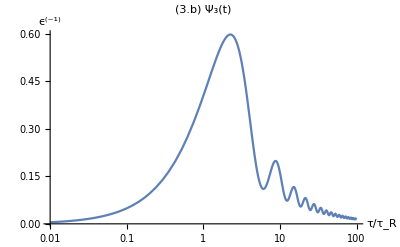

```mathematica
LogLinearPlot[ϵ1[τ],{τ,0.01,100},PlotRange->Full,AxesLabel->{"τ/τ_R","ϵ^(-1)"},PlotLabel->"(3.b) Ψ_3(t)"]
```